```mathematica
Ex vivo Magnetic Resonance Diffusion Weighted Imaging in Congenital Heart Disease,an Insight into the Microstructures of Tetralogy of Fallot, Biventricular and Univentricular Systemic Right Ventricle


Please, acknowledge the work by citing the article entitled 
Ex vivo Magnetic Resonance Diffusion Weighted Imaging in Congenital Heart Disease,an Insight into the Microstructures of Tetralogy of Fallot,Biventricular and Univentricular Systemic Right Ventricle (Tous et al, 2020)
from the Journal of Cardiovascular Magnetic Resonance Imaging. This sequence was part of a comparison between SE monopolar,SE bipolar, STEAM monopolar, TRSE and TRSE adjusted to scan long term (~40 years)formalin fixed specimens with low T2 (~20ms). The scans were performed on a 3T Skyra bought in the early 2010(43mT/m gradient amplitude, 180 mT/m/ms slew rate).

STEAM monopolar:
```

```mathematica
Author Names:Cyril Tous 1,2,Thomas L.Gentles 3,Alistair A.Young 1,4,Beau Pontré 1
Author Affiliations:
1Department of Anatomy and Medical Imaging,University of Auckland,Auckland,New Zealand
2Laboratory of Clinical Image Processing Le Centre de Recherche du Centre Hospitalier de l’Université de Montréal,Canada
3Green Lane Paediatric and Congenital Cardiac Service,Starship Children’s Hospital,Auckland,New Zealand
4Department of Biomedical Engineering,King’s College London,UK


Corresponding Author Info:
Beau Pontré,
Department of Anatomy and Radiology,
University of Auckland,
b.pontre@auckland.ac.nz

Cyril Tous
cyriltous@gmail.com

(* modified mathematica from (Mattiello et al, 1995) and  (Zubkov et al, 2014) *)
Date         :   22/09/2017;
Input        :    Known sequence diagram of the diffusion sequence  with the timing and  gradients' amplitude;
Output   :     B matrix [ndir, 6]  with ndir the number of diffusion directions, and Bmatrix[1,:]= [Bxx, Byy, Bzz, 2Bxy, 2Bxz, 2Byz];
Goal         :
=>Generating the B matrix from the known sequence diagram; 
    =>determining M0=F=Integral(g(t)), M1=Integral(t*g(t)), M2=Integral(t^2*g(t)) for the zeroth moment, first moment, second moment;
    => Calculating velocity shift Kv=γ*M1,d=Integral(F^2), Maxwell gradient moment =Integral(g(t)^2);

method  :      References:
-'Spin Diffusion Measurements:Spin Echoes in the Presence of a Time-Dependent Field Gradient' (STEjskal and Tanner, 1965);
-'Tissue Perfusion in Humans Studied by Fourier Velocity Distribution, Line Scan, and Echo Planar Imaging'(Feinberg, 1990);
- 'Analytical expressions for the b matrix in NMR diffusion Imaging and Spectroscopy' (Mattiello et al, 1993);
- 'Estimation of the Effective Self Diffusion TEnsor from the NMR Spin Echo' (Basser et al, 1993);
- 'Part II Analytical Calculation of the b Matrix in Diffusion Imaging'(Mattiello et al, 1995); => (Mathematica);
- 'Pusled-Field Gradient Nuclear Magnetic Resonance as a tool for studying translational diffusion:Part 1Basic Theory' (Price 1997);
- 'The b matrix in diffusion TEnsor echo planar imaging' (Mattiello et al, 1997);
-'Reduction of eddy-current-induced distortion in diffusion MRI using a twice-refocused spin echo'(Reese,2003);
-'Handbook of MRI Pulse Sequences (Bernstein, King, Zhou, 2004)'
-'Double spin echo diffusion weighting with a modified eddy current adjustment'(Finsterbusch, 2010);
- 'Efficient and precise calculation of the b matrix elements in diffusion weigthed imaging pulse sequences' (Zubkov et al, 2014);
=> (Mathematica);
-'Orthogonalizing crusher and diffusion-encoding gradients to suppress undesired echo pathways in the twice-refocused spin echo diffusion sequence'(Nagy, 2014);
```

```mathematica
(*
      90         δ               180               δ                  echo
   _        ______           _             _______              
   ||       |      |          ||            |      |               ||||
---------------------------------------------------------------
*)
"Pulsed Field Gradient Nuclear Magnetic resonance as a Tool for Studying Translational Diffusion: Part 1. Basic Theory(Price, 1996)";
ClearAll["Global`*"]
F[g_,ti_]=∫_ti^t gⅆtd;
g1=0;
l1=0;
F1=F[g1,l1];

l2=t1;
g2=g;
F2=Replace[F1,t->l2,All] + F[g2,l2];

l3=t1+δ;
g3=0;
F3=Replace[F2,t->l3,All] +  F[g3,l3];

l4=t1+ Δ;
g4=g;
F4=Replace[F3,t->l4,All] +  F[g4,l4] ;

l5=t1+Δ + δ ;
g5=0;
F5=Replace[F4,t->l5,All]+F[g5,l5];

l6=2*τ;

(* Define the function "f" [=F(tau)] *)
f=Replace[F3,t->τ,All];

(* Define the integral of F between τ and 2τ *)
(* FINT = Simplify[∫_τ^l4 F3 ⅆt+ ∫_l4^l5 F4ⅆt+ ∫_l5^l6 F5ⅆt ] *)
FINT= Simplify[ Integrate[F3,{t,τ,l4}]+Integrate[F4,{t,l4,l5}]+Integrate[F5,{t,l5,l6}]];

(* Define the integral of F^2 between 0 and 2τ *)
FSQINT = Simplify[Integrate[F1^2,{t,l1,l2}]+Integrate[F2^2,{t,l2,l3}]+Integrate[F3^2,{t,l3,l4}]+Integrate[F4^2,{t,l4,l5}]
		+Integrate[F5^2,{t,l5,l6}]];

(* Define the function to give the STEjskal and Tanner relationaship and simplify the result *)
logE=Simplify[-γ^2*D*(FSQINT-4*f*FINT+4*f^2*τ )];
(* D g^2 γ^2 δ^2 (δ/3-Δ)*)
```

```mathematica
Test b value according different δ and G;
```

```mathematica
ClearAll["Global`*"]

γ=2*Pi*42.5756*1000000*10^-4;(*[/G/s]*)
ϵ=400*10^-6;
TM=150000*10^-6;
GS180FLT=(3440+2*400)*10^-6;
crushers=(650+240)*2*10^-6;
Δ=(GS180FLT+crushers+δ+2ϵ+TM);
bvalue=(γ^2 G^2(δ^2(Δ-δ/3)+ϵ^3/30-(δ ϵ^2)/6))/.G-> 42*10^-2;
y=ComplexExpand[Re[Solve[bvalue==800.,δ]]];
(* 6280 *)
B[G_,δ_]=γ^2 G^2(δ^2(Δ-δ/3)+ϵ^3/30-(δ ϵ^2)/6);

(*Plot[{B[Gdiff,6280*3/2*10^-6],B[Gdiff,6280*10^-6],B[Gdiff,6280*4/5*10^-6],B[Gdiff,6280/2*10^-6],Callout[800.,b800]},{Gdiff,0*10^-2,50*10^-2},PlotLegends->{delta=6280*3/2,delta=6280.,delta=6280*4/5,delta=6280/2},AxesLabel->{β[Gauss],b[s/mm^2]}]*)
(*-Graphics-*)
```

```mathematica
The same b value  can occur for different acquisition parameters δ  or/and G;
```

```mathematica
Gradient amplitude and sequence timing;
 "code adapted from: 'Efficient and precise calculation of the b matrix elements in diffusion weigthed imaging pulse sequences' (Zubkov et al, 2014); (Mathematica)";
```

```mathematica
ClearAll["Global`*"]
trap[δ_,ϵ_,β_,t_]=β*Clip[UnitTriangle[2t/(δ+ϵ)-1]*(ϵ+δ)/(2ϵ)]; (*defining the trapezoidal gradient pulse*)

ScaleDiagram=50.;
ndir=32;
bvalueInput=800;

(*our values (2017);*)
γ=2.*Pi*42.5756*1000000;
ϵ=400.*10^-6;
shiftADC=500.*10^-6;
tReadout=7700.*10^-6;
rampReadout=10.*10^-6;
TM=150000.*10^-6; 
GmaxDiff=42.*10^-2;
GmaxCrush=19.79*10^-2;
RampGrdp=60.*10^-6;
RampGpe=50.*10^-6;
RampGsrf=120.*10^-6;
RampCrushers=240.*10^-6;
PhaseDispersionCrushers=6.;
SliceThickness=4.; (*mm*)

(* Bernstein et al, handbook of MRI pusle sequences *)
(* Duration of the crushers' gradients according the phse dispersion input. *)
AreaCrushers=PhaseDispersionCrushers*Pi/(γ*0.000001*SliceThickness*0.001);
DurationCrushers=N[Round[AreaCrushers/(GmaxCrush*10^2*0.001)]];

(* For the graph's plot, dslice and kvslice ;*)
(*SignDelta={1.,1.};*)

(*For the bmatrix calculation;*)
SignDelta={1.,-1.};

(* " Optimal strategies for measuring diffusion in anisotropic systems by magnetic resonance imaging" (Jones, 1999)*)
(* we have sorted the gradient encoding scheme to alternate between the gradient axis at each new direction*)
(* 6dir Electrostatic Repulsions *)
GradDiff6={{-0.887689,-0.101313,-0.449159},
{0.152552, 0.851204, 0.502175},
{-0.006226, 0.064447,-0.997902},
{0.789559,-0.384929,-0.47794},
{-0.399917, 0.82842,-0.392157},
{0.636679, 0.653135,-0.409945}}//MatrixForm;

(* 32dir:Electrostatic Repulsion scheme *)
GradDiff32={{0.978177,-0.099085,-0.182624},
{0.004364,-0.977355, 0.211562},
{0.058008,-0.049572,-0.997085},
{-0.951171, 0.161172,-0.263244},
{0.117967,-0.96576,-0.231065},
{-0.20677, 0.303548,-0.93011},
{-0.944892,-0.293928,-0.144174},
{-0.353468,-0.934011,-0.05181},
{-0.435353,-0.090815,-0.895667},
{0.890215, 0.360105,-0.279001},
{0.519013,-0.854199,-0.031151},
{-0.102942,-0.448113,-0.88803},
{0.841861,-0.525064,-0.124811},
{0.378146, 0.845537,-0.376926},
{0.478308, 0.041353,-0.877218},
{0.801211, 0.063809,-0.59497},
{-0.281684,-0.832306,-0.477411},
{0.231306, 0.428135,-0.873612},
{-0.80002,-0.223072,-0.556963},
{-0.348364,-0.817823, 0.458049},
{0.37987,-0.40282,-0.832727},
{-0.760744, 0.566441,-0.316879},
{0.11871,-0.750307,-0.650344},
{-0.49852,-0.514078,-0.697998},
{0.74759,-0.362889,-0.556256},
{0.029535,-0.733272, 0.679294},
{-0.467151 ,0.549242,-0.692895},
{0.716315,-0.197382, 0.669278},
{0.514837,-0.726299,-0.455448},
{-0.697256,-0.653755,-0.294005},
{-0.680714,-0.715159, 0.15867},
{0.599777, 0.492419,-0.630707}}//MatrixForm;

(* 64dir Electrostatic Repulsions *)
GradDiff64={{-0.997625,-0.026724, 0.063488},
{-0.154722, 0.987867, 0.013398},
{-0.015834,-0.014472,-0.99977},
{0.963101,-0.267540, 0,.029315},
{-0.12564,-0.9854060, 0.114845},
{0.065038, 0.29541300,-0.953153},
{-0.959665,-0.2166720,-0.179153},
{0.006778,-0.955284,-0.295611},
{0.30751, 0.090828,-0.9472},
{0.949992,-0.0861430,0.300156},
{-0.27859,-0.9485760,-0.150306},
{-0.055576,-0.316879,-0.946836},
{0.927325,-0.21633400,-0.305397},
{-0.132838, 0.93592300,-0.326194},
{-0.3284670,-0.0346480,-0.94388},
{0.926285, 0.117378,-0.358076},
{-0.419397, 0.89762,0.135587},
{0.2760480,-0.2176970,-0.936165},
{0.923215, 0.3629970,-0.126124},
{0.208215, 0.891081,-0.403263},
{-0.239236, 0.2854840,-0.928044},
{0.83921,-0.379789,0.389213},
{0.446139, 0.883423,-0.143262},
{-0.370819,-0.344175,-0.862576},
{-0.837437, 0.5327130,-0.12213},
{-0.423944, 0.882753,-0.202533},
{0.218118,-0.5048100,-0.835219},
{-0.835774,-0.104423,-0.539052},
{0.291451,-0.8639870,-0.410588},
{0.304862, 0.464001,-0.831722},
{-0.834875, 0.510044, 0.206975},
{-0.141862,-0.824696,-0.547496},
{-0.020026, 0.576391,-0.816928},
{-0.830952,-0.381428,-0.405009},
{-0.407192,-0.82266700,-0.396753},
{-0.522214, 0.248724,-0.815738},
{0.827364, 0.548564, 0.12061},
{-0.063469 ,0.795508,-0.60261},
{0.580539,-0.068549,-0.811342},
{0.797023,-0.136705,-0.588273},
{0.601245, 0.789791, 0.121382},
{0.539573, 0.252383,-0.803221},
{0.792823, 0.455369,-0.405057},
{-0.378698, 0.766359,-0.518923},
{-0.122014,-0.589755,-0.798312},
{0.768559 ,0.1941,-0.609624},
{0.66151,-0.749911,-0.006173},
{-0.607712,-0.077141,-0.790402},
{-0.762479 ,0.1863260,-0.619604},
{0.137929,-0.7466040,-0.650813},
{0.532848,-0.37023500,-0.760920},
{0.734088,-0.4443650,-0.513473},
{-0.524955,-0.74215100, 0.416694},
{-0.332668 ,0.55742500,-0.760663},
{0.726209, 0.66617000,-0.169821},
{0.611904,-0.7124550,-0.343485},
{-0.637493,-0.37653400,-0.672179},
{0.269452, 0.7119370,-0.648492},
{-0.413285,-0.619494,-0.6674},
{-0.651714,-0.630831,-0.421095},
{-0.645004 ,0.682074,-0.344595},
{0.456964,-0.642255,-0.61538},
{0.576347, 0.522314,-0.6285},
{-0.611822 ,0.50219,-0.611129}}//MatrixForm;

Switch[ndir,4,GradDiff=GradDiff4,6,GradDiff=GradDiff6,32,GradDiff=GradDiff32,64,GradDiff=GradDiff64];

(*"Orthogonalizing crusher and diffusion-encoding gradients to suppress undesired echo pathways in the twice-refocused spin echo diffusion sequence(Nagy, 2014)"*)
dir=1;
While[dir<ndir+1,
if [((Abs[GradDiff[[1,dir,1]]]+Abs[GradDiff[[1,dir,3]]])≠0.),
CoordCrusherX[dir]=-Sign[GradDiff[[1,dir,1]]*GmaxDiff*10^2]*Sign[GradDiff[[1,dir,3]]*GmaxDiff*10^2]*
(1-Abs[GradDiff[[1,dir,1]]]/(Abs[GradDiff[[1,dir,1]]]+Abs[GradDiff[[1,dir,3]]]));
CoordCrusherY[dir]=0.;
CoordCrusherZ[dir]=1.-Abs[CoordCrusherX[dir]];
,
CoordCrusherX[dir]=GradDiff[[1,dir,1]];
CoordCrusherY[dir]=0.;
CoordCrusherZ[dir]=1.-Abs[CoordCrusherX[dir]]
];

(* (our values, 2017) *)
subamp[dir]={Gsl90->0.075*10^2*10^-6,Gsl180->0.06*10^2*10^-6,Gsrf->-0.1982*10^2*10^-6, Gpe->0.*10^2*10^-6, Grdp->-0.1071*10^2*10^-6, Gro->0.0153*10^2*10^-6,
Gcr->GmaxCrush*CoordCrusherX[dir]*10^2*10^-6, Gcp->GmaxCrush*CoordCrusherY[dir]*10^2*10^-6,Gcs->GmaxCrush*CoordCrusherZ[dir]*10^2*10^-6,Gdr->GmaxDiff*GradDiff[[1,dir,1]]*10^2*10^-6, Gdp->GmaxDiff*GradDiff[[1,dir,2]]*10^2*10^-6,Gds->GmaxDiff*GradDiff[[1,dir,3]]*10^2*10^-6};
dir++];

(* (our values, 2017) *)
time1={TE->29140*10^-6+TM,Gsl90t->2960*10^-6,Gsl180t->3840*10^-6,Grdpt->560*10^-6+RampGrdp,Gpet->580*10^-6+RampGpe,Gsrft->440*10^-6+RampGsrf,Grot->tReadout+shiftADC+rampReadout,Crut->DurationCrushers*10^-6};

Calculation of δ 1according inputs;
bvalue=(γ^2*G^2*(δ^2*(Δ-δ/3)+ϵ^3/30-δ*ϵ^2/6))/.G->(GmaxDiff*10^2*10^-6)/.Δ->(δ+ϵ)+2Crut+(Gsl180t+ϵ)+TM/.time1/.subamp[1];
deltas=ComplexExpand[Re[Solve[bvalue==bvalueInput,δ]]];
deltas=Select[deltas[[All,1,2]],#>0&];
delta=Ceiling[deltas[[1]]*10^6,10]*10^-6;
time1=N[Append[time1,δ->delta]];

Interduration=N[Max[(Gsl90t-ϵ)/2+ϵ+Max[Gpet+RampGpe,Gsrft+RampGsrf],Grdpt+RampGrdp+tReadout/2+shiftADC+rampReadout]/.time1];

time2=N[{t2->(Gsl90t+ϵ)/2.,
t21->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf],
t31->Interduration,
t41a->Interduration+(δ+ϵ),
t5a->Interduration+(δ+ϵ)+Crut+RampCrushers-ϵ,
t41b->Interduration+(δ+ϵ)+Crut+RampCrushers-ϵ+Gsl180t,
t42a->Interduration+(δ+ϵ)+TM,
t5b->Interduration+(δ+ϵ)+Crut+RampCrushers-ϵ+TM,
t42b->Interduration+(δ+ϵ)+Crut+RampCrushers-ϵ+Gsl180t+TM,
t32->Interduration+(δ+ϵ)+2Crut+2RampCrushers-ϵ+Gsl180t+TM,
t6->Interduration+2(δ+ϵ)+2Crut+2RampCrushers-ϵ+Gsl180t+TM,
t7->Interduration+2(δ+ϵ)+2Crut+2RampCrushers-ϵ+Gsl180t+TM+Grdpt+RampGrdp,
t8->Interduration+2(δ+ϵ)+2Crut+2RampCrushers-ϵ+Gsl180t+TM+Grdpt+RampGrdp+tReadout/2.+shiftADC+rampReadout}/.time1];

Δ=t32-t31;

time3=time2/.time1;
subs[g_]:=g/.time1;

T1=(Interduration+(δ+ϵ)+Crut+RampCrushers+(Gsl180t-ϵ)/2)/.time1;
T2=(T1+TM)/.time1;
bvalue=subs[(γ^2*G^2*(δ^2*(Δ-δ/3)+ϵ^3/30-δ*ϵ^2/6))/.G->(GmaxDiff*10^2*10^-6)]/.time3/.subamp[1];(* 800.54 *)
```

```mathematica
Defining the STEAM gradient pulse and its integral;
```

```mathematica
FiInt[f_,ll_,ul_]:=Integrate[f,{t,ll,ul},Assumptions->{ll>0,ul>0,offs>0,wid>ϵ,wid>0,ϵ>0}] ;

integral;
idtrap[δ_,ϵ_,β_,ll_,ul_]=Simplify[Refine[FiInt[trap[wid,ϵ,amp,t-ll],ll,ul],Assumptions->{wid>0,ϵ>0,ul>0,wid>ϵ}]]/.wid->δ/.amp->β;
```

```mathematica
READ;
dir=1;
While[dir<ndir+1,
AmpIntReadAtT1[dir]=subs[idtrap[δ,ϵ,SignDelta[[1]]*Gdr,t31,T1]+idtrap[Crut,RampCrushers,Gcr,t41a,T1]]/.time3/.subamp[dir];

Gread[t_,dir]=subs[trap[δ,ϵ,SignDelta[[1]]*Gdr,t-t31]+trap[Crut,RampCrushers,Gcr,t-t41a]+trap[Crut,RampCrushers,Gcr,t-t41b]+trap[Crut,RampCrushers,Gcr,t-t42a]+trap[Crut,RampCrushers,Gcr,t-t42b]+trap[δ,ϵ,SignDelta[[2]]*Gdr,t-t32]+trap[Grdpt,RampGrdp,Grdp,t-t6]+trap[Grot,RampGrdp,Gro,t-t7]]/.time3/.subamp[dir];

Fread[t_,dir]=Simplify[subs[(1-UnitStep[t-T2])*(idtrap[δ,ϵ,SignDelta[[1]]*Gdr,t31,t]+idtrap[Crut,RampCrushers,Gcr,t41a,t])+
UnitStep[t-T2]*(-AmpIntReadAtT1[dir]+idtrap[Crut,RampCrushers,Gcr,t42b,t]+
idtrap[δ,ϵ,SignDelta[[2]]*Gdr,t32,t]+idtrap[Grdpt,RampGrdp,Grdp,t6,t]+idtrap[Grot,RampGrdp,Gro,t7,t])]/.time3/.subamp[dir]];
dir++];

dir=1;
{subs[Gread[t,1]/.t->TE]/.time3/.subamp[1],subs[(γ*Fread[t,1]/.t->TE)]/.time3/.subamp[1],subs[(γ*Fread[t,1]/.t->TE)^2]/.time3/.subamp[1]}//AbsoluteTiming;
```

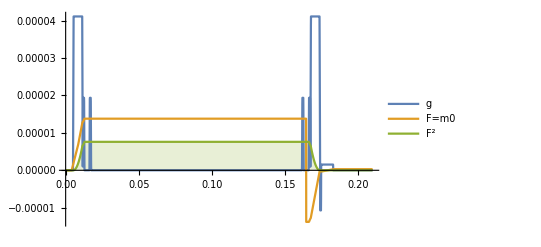
```mathematica
dirPlot=1;
(*Plot[{subs[Gread[t,dirPlot]]/.time3/.subamp[dirPlot],ScaleDiagram*subs[Fread[t,dirPlot]]/.time3/.subamp[dirPlot],(200ScaleDiagram)^2*subs[(Fread[t,dirPlot])^2]/.time3/.subamp[dirPlot]},{t,0,210000.*10^-6},PlotRange->Full,Filling->{3->Axis},PlotLegends->{"g","F=m0","F^2"}]//AbsoluteTiming*)
(*-Graphics-*)
```

```mathematica
PHASE;
dir=1;
While[dir<ndir+1,
AmpIntPhaseAtT1[dir]=subs[ idtrap[Gpet,RampGpe,Gpe,t2,T1]+idtrap[δ,ϵ,SignDelta[[1]]*Gdp,t31,T1]+idtrap[Crut,RampCrushers,Gcp,t41a,T1]]/.time3/.subamp[dir];

Gphase[t_,dir]=subs[trap[Gpet,RampGpe,Gpe,t-t2]+trap[δ,ϵ,SignDelta[[1]]*Gdp,t-t31]+trap[Crut,RampCrushers,Gcp,t-t41a]+trap[Crut,RampCrushers,Gcp,t-t41b]+trap[Crut,RampCrushers,Gcp,t-t42a]+trap[Crut,RampCrushers,Gcp,t-t42b]+trap[δ,ϵ,SignDelta[[2]]*Gdp,t-t32]]/.time3/.subamp[dir];

Fphase[t_,dir]=Simplify[subs[(1-UnitStep[t-T2])*(idtrap[Gpet,RampGpe,Gpe,t2,t]+idtrap[δ,ϵ,SignDelta[[1]]*Gdp,t31,t]+idtrap[Crut,RampCrushers,Gcp,t41a,t])+
UnitStep[t-T2]*(-AmpIntPhaseAtT1[dir]+idtrap[Crut,RampCrushers,Gcp,t42b,t]+
idtrap[δ,ϵ,SignDelta[[2]]*Gdp,t32,t])]/.time3/.subamp[dir]];
dir++];
dir=1;

dirPlot=1;
{subs[Gphase[t,dirPlot]/.t->TE]/.time3/.subamp[dirPlot],subs[(γ*Fphase[t,dirPlot]/.t->TE)]/.time3/.subamp[dirPlot],subs[(γ*Fphase[t,dirPlot]/.t->TE)^2]/.time3/.subamp[dirPlot]}//AbsoluteTiming;
```

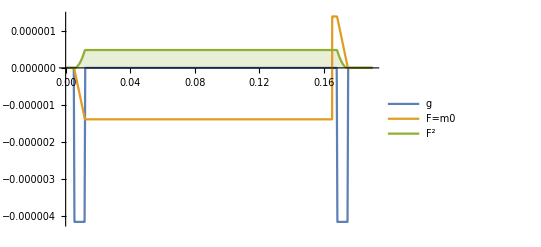
```mathematica
dirPlot=1;
(*Plot[{subs[Gphase[t,dirPlot]]/.time3/.subamp[dirPlot],ScaleDiagram*subs[Fphase[t,dirPlot]]/.time3/.subamp[dirPlot],(500ScaleDiagram)^2*subs[(Fphase[t,dirPlot])^2]/.time3/.subamp[dirPlot]},{t,0.*10^-6,190000.*10^-6},PlotRange->Full,Filling->{3->Axis},PlotLegends->{"g","F=m0","F^2"}]//AbsoluteTiming*)
(*-Graphics-*)
```

```mathematica
SLICE;
dir=1;
While[dir<ndir+1,
AmpIntSliceAtt2[dir]=subs[idtrap[Gsl90t,ϵ,Gsl90,t2,T1]/2]/.time3/.subamp[dir];

AmpIntSliceAtT1[dir]=subs[idtrap[Gsl90t,ϵ,Gsl90,t2,T1]/2+idtrap[Gsrft,RampGsrf,Gsrf,t2,T1]+idtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,T1]+idtrap[Crut,RampCrushers,Gcs,t41a,T1]+idtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,t5a,T1]]/.time3/.subamp[dir];

Gslice[t_,dir]= subs[trap[Gsl90t,ϵ,Gsl90,t+t2]+trap[Gsrft,RampGsrf,Gsrf,t-t2]+trap[δ,ϵ,SignDelta[[1]]*Gds,t-t31]+trap[Crut,RampCrushers,Gcs,t-t41a]+trap[Gsl180t,ϵ,Gsl180,t-t5a]+trap[Crut,RampCrushers,Gcs,t-t42a]+trap[Crut,RampCrushers,Gcs,t-t41b]+trap[Gsl180t,ϵ,Gsl180,t-t5b]+trap[Crut,RampCrushers,Gcs,t-t42b]+trap[δ,ϵ,SignDelta[[2]]*Gds,t-t32]]/.time3/.subamp[dir];

Fslice[t_,dir]=Simplify[subs[((1-UnitStep[t-t2])*idtrap[Gsl90t,ϵ,Gsl90,t2,t+t2]+UnitStep[t-t2]*(AmpIntSliceAtt2[dir]+idtrap[Gsrft,RampGsrf,Gsrf,t2,t]))+(1-UnitStep[t-T2])*(idtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,t]+idtrap[Crut,RampCrushers,Gcs,t41a,t]+idtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,t5a,t])+UnitStep[t-T2]*(-AmpIntSliceAtT1[dir]+idtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,T2,t]+idtrap[δ,ϵ,SignDelta[[2]]*Gds,t32,t]+idtrap[Crut,RampCrushers,Gcs,t42b,t])]/.time3/.subamp[dir]];
dir++];
dir=1;

dirPlot=1;
{subs[Gslice[t,1]/.t->TE]/.time3/.subamp[1],subs[(γ*Fslice[t,1]/.t->TE)]/.time3/.subamp[1],subs[(γ*Fslice[t,1]/.t->TE)^2]/.time3/.subamp[1]}//AbsoluteTiming;
```

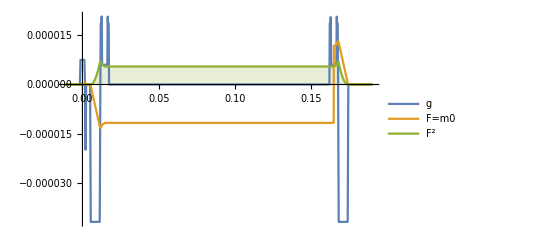
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time3/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time3/.subamp[dirPlot],(200ScaleDiagram)^2*subs[(Fslice[t,dirPlot])^2]/.time3/.subamp[dirPlot]},{t,-11000.*10^-6,190000.*10^-6},PlotRange->Full,Filling->{3->Axis},PlotLegends->{"g","F=m0","F^2"}]//AbsoluteTiming*)

(*-Graphics-*)
```

```mathematica
"Maxwell gradient moment= integral(g^2)";
dir=1;
While[dir<ndir+1,
AmpMxIntSliceAtt2[dir]=subs[idtrap[Gsl90t,ϵ,Gsl90^2,t2,T1]]/.time3/.subamp[dir];

AmpMxIntSliceAtT1[dir]=subs[idtrap[δ,ϵ,SignDelta[[1]]*Gds^2,t31,T1]+idtrap[Crut,RampCrushers,Gcs^2,t41a,T1]+idtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180^2,t5a,T1]]/.time3/.subamp[dir];

MxFslice[t_,dir]=Simplify[subs[(1-UnitStep[t-t2])*idtrap[Gsl90t,ϵ,Gsl90^2,t2,t+t2]+UnitStep[t-t2]*(+idtrap[Gsl90t,ϵ,Gsl90^2,t2,t+t2]-idtrap[Gsrft,RampGsrf,Gsrf^2,t2,t])+(1-UnitStep[t-T2])*(idtrap[δ,ϵ,SignDelta[[1]]*Gds^2,t31,t]+idtrap[Crut,RampCrushers,Gcs^2,t41a,t]+idtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180^2,t5a,t])+UnitStep[t-T2]*(-AmpMxIntSliceAtT1[dir]+idtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180^2,T2,t]+idtrap[δ,ϵ,SignDelta[[2]]*Gds^2,t32,t]+idtrap[Crut,RampCrushers,Gcs^2,t42b,t])]/.time3/.subamp[dir]];
dir++];
dir=1;

dirPlot=3;
{subs[Gslice[t,dirPlot]/.t->TE]/.time3/.subamp[dirPlot],subs[(MxFslice[t,dirPlot]/.t->TE)]/.time3/.subamp[dirPlot]};
```

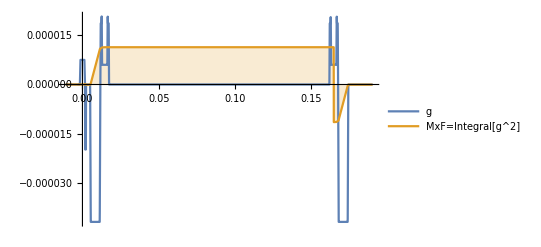
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time3/.subamp[dirPlot],(20ScaleDiagram)^2*subs[MxFslice[t,dirPlot]]/.time3/.subamp[dirPlot]},{t,-11000.*10^-6,190000.*10^-6},PlotRange->Full,Filling->{2->Axis},PlotLegends->{"g","MxF=Integral[g^2]"}]//AbsoluteTiming*)
(*-Graphics-*)
```

```mathematica
integral(integral);
i2dtrap[δ_,ϵ_,β_,ll_,ul_,a_,b_]=Simplify[Refine[FiInt[idtrap[δ,ϵ,amp,ll,ul],a,b],Assumptions->{wid>0.,a≥0.,b>a,b>0.,a<ul<b,ll≥0.,ϵ>0.,ul>0.,β≥0.,wid>ϵ}]]/.wid->δ/.amp->β;
dir=1;
While[dir<ndir+1,
Amp2IntSliceAtt2[dir]=subs[i2dtrap[Gsl90t,ϵ,Gsl90,t2,T1,0,TE]/2]/.time3/.subamp[dir];
Amp2IntSliceAtT1[dir]=subs[ i2dtrap[Gsl90t,ϵ,Gsl90,t2,T1,0,TE]/2.+i2dtrap[Gsrft,RampGsrf,Gsrf,t2,T1,0,TE]+i2dtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,T1,0,TE]+i2dtrap[Crut,RampCrushers,Gcs,t41a,T1,0,TE]+i2dtrap[(Gsl180t+ϵ)/2,RampGsl180,Gsl180,t5a,T1,0,TE]]/.time3/.subamp[dir];

IntFslice[t_,dir]=(1-UnitStep[t-t2])*i2dtrap[Gsl90t,ϵ,Gsl90,t2,t+t2,0,TE]+UnitStep[t-t2]*(Amp2IntSliceAtt2[dir]+i2dtrap[Gsrft,RampGsrf,Gsrf,t2,t,0,TE])+
(1-UnitStep[t-T2])*(i2dtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,t,0,TE]+i2dtrap[Crut,RampCrushers,Gcs,t41a,t,0,TE]+i2dtrap[(Gsl180t+ϵ)/2,RampGsl180,Gsl180,t5a,t,0,TE])+ UnitStep[t-T2]*(-Amp2IntSliceAtT1[dir]+i2dtrap[(Gsl180t+ϵ)/2,RampGsl180,Gsl180,T2,t,0,TE]+i2dtrap[Crut,RampCrushers,Gcs,t42b,t,0,TE]+i2dtrap[δ,ϵ,SignDelta[[2]]*Gds,t32,t,0,TE]);
dir++];
dir=1;
```

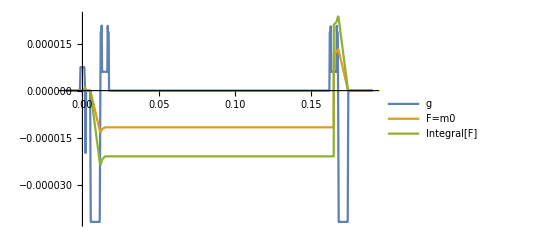
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time3/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time3/.subamp[dirPlot],10ScaleDiagram*subs[IntFslice[t,dirPlot]]/.time3/.subamp[dirPlot]},{t,-11000*10^-6,190000*10^-6},PlotRange->Full,PlotLegends->{"g","F=m0","Integral[F]"}]*)
(*-Graphics-*)
```

```mathematica
d=integral[integral^2];
iSqidtrap[δ_,ϵ_,β_,ll_,ul_,a_,b_]=Simplify[Refine[FiInt[(idtrap[δ,ϵ,amp,ll,ul])^2,a,b],Assumptions->{wid>0.,a≥0.,b>a,b>0.,a<ul<b,ll≥0.,ϵ>0.,ul>0.,β≥0.,wid>ϵ}]]/.wid->δ/.amp->β;
dir=1;
While[dir<ndir+1,
Amp2IntSqSliceAtt2[dir]=subs[iSqidtrap[Gsl90t,ϵ,Gsl90,t2,T1,0,TE]/2]/.time3/.subamp[dir];

Amp2IntSqSliceAtT1[dir]=subs[ iSqidtrap[Gsl90t,ϵ,Gsl90,t2,T1,0,TE]/2.+iSqidtrap[Gsrft,RampGsrf,Gsrf,t2,T1,0,TE]+iSqidtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,T1,0,TE]+iSqidtrap[Crut,RampCrushers,Gcs,t41a,T1,0,TE]+iSqidtrap[(Gsl180t+ϵ)/2,RampGsl180,Gsl180,t5a,T1,0,TE]]/.time3/.subamp[dir];

IntSqFslice[t_,dir]=(1-UnitStep[t-t2])*iSqidtrap[Gsl90t,ϵ,Gsl90,t2,t+t2,0,TE]+UnitStep[t-t2]*(Amp2IntSqSliceAtt2[dir]+iSqidtrap[Gsrft,RampGsrf,Gsrf,t2,t,0,TE])+
(1-UnitStep[t-T2])*(iSqidtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,t,0,TE]+iSqidtrap[Crut,RampCrushers,Gcs,t41a,t,0,TE]+iSqidtrap[(Gsl180t+ϵ)/2,RampGsl180,Gsl180,t5a,t,0,TE])+ UnitStep[t-T2]*(-Amp2IntSqSliceAtT1[dir]+iSqidtrap[(Gsl180t+ϵ)/2,RampGsl180,Gsl180,T2,t,0,TE]+iSqidtrap[Crut,RampCrushers,Gcs,t42b,t,0,TE]+iSqidtrap[δ,ϵ,SignDelta[[2]]*Gds,t32,t,0,TE]);

dir++];
dir=1;
```

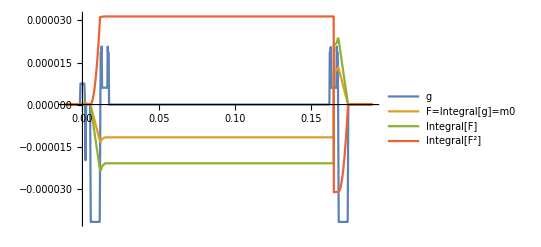
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time3/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time3/.subamp[dirPlot],10ScaleDiagram*subs[IntFslice[t,dirPlot]]/.time3/.subamp[dirPlot],(1000ScaleDiagram)^2*subs[IntSqFslice[t,dirPlot]]/.time3/.subamp[dirPlot]},{t,-11000*10^-6,190000*10^-6},PlotRange->Full,PlotLegends->{"g","F=Integral[g]=m0","Integral[F]","Integral[F^2]"}]*)
(*-Graphics-*)
```

```mathematica
Bmatrix;
(*set SignDelta={1.,-1.};*)
dir=1;
While[dir<ndir+1,
(F[t_,dir]={{Fread[t,dir]},{Fphase[t,dir]},{Fslice[t,dir]}})//MatrixForm;

fread[dir]=Fread[t,dir]/.t->T2;
fphase[dir]=Fphase[t,dir]/.t->T2;
fslice[dir]=Fslice[t,dir]/.t->T2;
(f[dir]={{fread[dir]},{fphase[dir]},{fslice[dir]}})//MatrixForm;

b1v[dir]=NIntegrate[F[t,dir].Transpose[F[t,dir]],{t, 0,T2}];
b2v[dir]=NIntegrate[(F[t,dir]-2f[dir]).Transpose[F[t,dir]-2f[dir]],{t,T2,N[TE/.time1]}];

dir++];
dir=1;
```

```mathematica
bTensor=Reap[Do[Sow[γ^2*(b1v[dir]+b2v[dir])],{dir,1,ndir}]][[2]]//MatrixForm;
bTrace=Transpose[Reap[Do[Sow[Tr[bTensor[[1,1,dir]]]],{dir,1,ndir}]][[2]]];
Mean[bTrace]; (* 795.01 *)
StandardDeviation[bTrace]; (* 84.45 *)
Bmatrix=Reap[Do[Sow[ {bTensor[[1,1,dir,1,1]], bTensor[[1,1,dir,2,2]], bTensor[[1,1,dir,3,3]], 2bTensor[[1,1,dir,1,2]], 2bTensor[[1,1,dir,1,3]], 2bTensor[[1,1,dir,2,3]]}],{dir,1,ndir}]][[2]];

(*Export["C:\\users\\Bmatrix_STEAMmp_32dir.xlsx",Bmatrix,"XLSX"];*)
```

```mathematica
Bmatrix display; 
Bmatrix=Transpose[Reap[Do[Sow[ {{bTensor[[1,1,dir,1,1]], bTensor[[1,1,dir,2,2]], bTensor[[1,1,dir,3,3]], 2bTensor[[1,1,dir,1,2]], 2bTensor[[1,1,dir,1,3]], 2bTensor[[1,1,dir,2,3]]}}],{dir,1,ndir}]][[2]]]//MatrixForm;
```

```mathematica
(* For the graph's plot, dslice and kvslice ;*)
(*set SignDelta={1.,1.};*)
dslice=γ^2*NIntegrate[F[t,1].Transpose[F[t,1]],{t, 0,N[TE/.time1]}];
dsliceTrace=Tr[dslice];
dsliceExp=γ^2*NIntegrate[F[t,1].Transpose[F[t,1]]*Exp[-t/0.030],{t, 0,N[TE/.time1]}]//MatrixForm;
Kvslice=γ*NIntegrate[t*Gslice[t,1],{t, 0,N[TE/.time1]}]//MatrixForm;
```

```mathematica
M0 and M1 and M2 ;
integral M1;
iM1dtrap[δ_,ϵ_,β_,ll_,ul_]=Simplify[Refine[FiInt[t*trap[wid,ϵ,amp,t-ll],ll,ul],Assumptions->{wid>0.,ϵ>0.,ul>0.,wid>ϵ}]]/.wid->δ/.amp->β;
```

```mathematica
dir=1;
While[dir<ndir+1,
AmpIntM1SliceAtt2[dir]=subs[iM1dtrap[Gsl90t,ϵ,Gsl90,t2,T1]/2]/.time3/.subamp[dir];

AmpIntM1SliceAtT1[dir]=subs[iM1dtrap[Gsl90t,ϵ,Gsl90,t2,T1]/2+iM1dtrap[Gsrft,RampGsrf,Gsrf,t2,T1]+iM1dtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,T1]+iM1dtrap[Crut,RampCrushers,Gcs,t41a,T1]+iM1dtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,t5a,T1]]/.time3/.subamp[dir];

M1slice[t_,dir]=Simplify[subs[((1-UnitStep[t-t2])*iM1dtrap[Gsl90t,ϵ,Gsl90,t2,t+t2]+UnitStep[t-t2]*(AmpIntM1SliceAtt2[dir]+iM1dtrap[Gsrft,RampGsrf,Gsrf,t2,t]))+(1-UnitStep[t-T2])*(iM1dtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,t]+iM1dtrap[Crut,RampCrushers,Gcs,t41a,t]+iM1dtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,t5a,t])+UnitStep[t-T2]*(-AmpIntM1SliceAtT1[dir]+iM1dtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,T2,t]+iM1dtrap[δ,ϵ,SignDelta[[2]]*Gds,t32,t]+iM1dtrap[Crut,RampCrushers,Gcs,t42b,t])]/.time3/.subamp[dir]];
dir++];
dir=1;
```

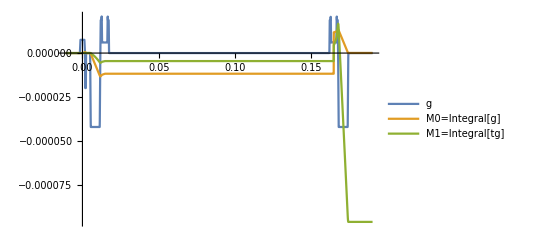
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time3/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time3/.subamp[dirPlot],50ScaleDiagram*subs[M1slice[t,dirPlot]]/.time3/.subamp[dirPlot]},{t,-11000*10^-6,190000*10^-6},PlotRange->Full,PlotLegends->{"g","M0=Integral[g]","M1=Integral[tg]"}]*)
(*-Graphics-*)
```

```mathematica
integral M2;
iM2dtrap[δ_,ϵ_,β_,ll_,ul_]=Simplify[Refine[FiInt[t^2*trap[wid,ϵ,amp,t-ll],ll,ul],Assumptions->{wid>0.,ϵ>0.,ul>0.,wid>ϵ}]]/.wid->δ/.amp->β;
```

```mathematica
dir=1;
While[dir<ndir+1,
AmpIntM2SliceAtt2[dir]=subs[iM2dtrap[Gsl90t,ϵ,Gsl90,t2,T1]/2]/.time3/.subamp[dir];

AmpIntM2SliceAtT1[dir]=subs[iM2dtrap[Gsl90t,ϵ,Gsl90,t2,T1]/2+iM2dtrap[Gsrft,RampGsrf,Gsrf,t2,T1]+iM2dtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,T1]+iM2dtrap[Crut,RampCrushers,Gcs,t41a,T1]+iM2dtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,t5a,T1]]/.time3/.subamp[dir];

M2slice[t_,dir]=Simplify[subs[((1-UnitStep[t-t2])*iM2dtrap[Gsl90t,ϵ,Gsl90,t2,t+t2]+UnitStep[t-t2]*(AmpIntM2SliceAtt2[dir]+iM2dtrap[Gsrft,RampGsrf,Gsrf,t2,t]))+(1-UnitStep[t-T2])*(iM2dtrap[δ,ϵ,SignDelta[[1]]*Gds,t31,t]+iM2dtrap[Crut,RampCrushers,Gcs,t41a,t]+iM2dtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,t5a,t])+UnitStep[t-T2]*(-AmpIntM2SliceAtT1[dir]+iM2dtrap[(Gsl180t+ϵ)/2,ϵ,Gsl180,T2,t]+iM2dtrap[δ,ϵ,SignDelta[[2]]*Gds,t32,t]+iM2dtrap[Crut,RampCrushers,Gcs,t42b,t])]/.time3/.subamp[dir]];
dir++];
dir=1;
```

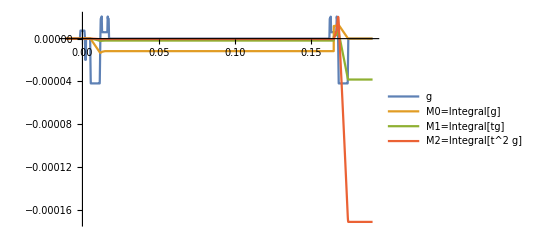
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time3/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time3/.subamp[dirPlot],20ScaleDiagram*subs[M1slice[t,dirPlot]]/.time3/.subamp[dirPlot],10 ScaleDiagram^2*subs[M2slice[t,dirPlot]]/.time3/.subamp[dirPlot]},{t,-11000*10^-6,190000*10^-6},PlotRange->Full,PlotLegends->{"g","M0=Integral[g]","M1=Integral[tg]","M2=Integral[t^2 g]"}]*)
(*-Graphics-*)
```